```mathematica
L=4;
f[x_,y_,t_]:=Piecewise[{{Exp[(-(x^2+y^2))/2],t<1/2}}]
Manipulate[DensityPlot[f[x,y,t],{x,-L,L},{y,-L,L},PlotRange->All,PlotPoints->50,ColorFunction->"Rainbow",Frame->False],{t,0,1}]
```

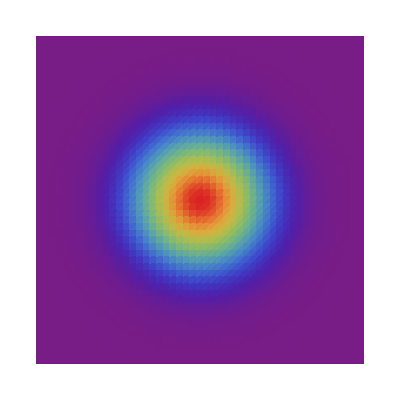
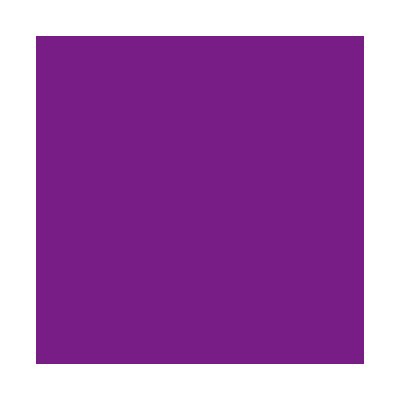
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

~/OneDrive - Rice University/Documents/Research/Optical tweezer on Fermi Hubbard/Notes//strobe.gif

```mathematica
Anime=Table[DensityPlot[f[x,y,t],{x,-L,L},{y,-L,L},PlotRange->All,PlotPoints->50,ColorFunction->"Rainbow",Frame->False],{t,0,0.9,0.1}]
Export["~/OneDrive - Rice University/Documents/Research/Optical tweezer on Fermi Hubbard/Notes//strobe.gif",Anime]
```